# Capital One Coders: Machine learning with Mathematica

### Agenda: 1)Intro to Mathematica 2)iSpy 3)Intro to Machine Learning 4)The Titanic

## Intro to Mathematica - Run the following examples

To use Mathematica do the following to run a ‘code block’
1) Click in between the code blocks
2) Click on the plus button between code blocks
3) Click on Wolfram Language Input
4) Type what you want Mathematica to compute
5) Press shift + enter to run your code block

Run the following examples

```mathematica
1+1
```

planes above

WolframAlphaQueryParseResults

```mathematica
Graphics3D[Sphere[]]
```

```mathematica
Plot3D[Cos[y] Sin[y]==Sin[x] Cos[x],{x,-2 Pi,1.5 Pi},{y,-2 Pi,1.5 Pi}]
```

how many dimes would fit on the surface of murcury

(lots of incredible examples of “1-liners” which Wolfram shares via Twitter here: https://twitter.com/wolframtap)

Links to check out some more cool examples

(https://www.wolfram.com/mathematica/new-in-8/free-form-linguistic-input/basic-examples.html) (https://www.wolfram.com/language/gallery/) (https://www.wolframalpha.com/examples/)  (http://demonstrations.wolfram.com/topic.html?limit=20&topic=For+Kids)

Activity: Do one of the following in new code blocks
1) Add two numbers
2) Print a cool 3D Graph (Hint: use Help | Wofram Documentation and find a category with functions that help you “see”)
3) Print the satellites above (Wolfram Alpha Query)
4) Print 2 of the examples

Some interesting things Mathematica can tell you about because it has a lot of curated history and data from Wofram Alpha ... e.g. Entity[“...”] function

```mathematica
Entity["Aircraft"]
```

(See http://blog.stephenwolfram.com/2017/11/what-is-a-computational-essay/)

GeoListPlot[WolframAlphaQueryParseResults]

-Graphics-

## iSpy

We’re going to use the Raspberry Pi camera to have Mathematica recognize images in the room (https://www.wolfram.com/language/11/neural-networks/out-of-core-image-classification.html?product=language) (https://www.wolfram.com/language/11/neural-networks/object-classification.html?product=language) 

For example:

```mathematica
ImageIdentify[-Graphics-]
```

Getting images from your raspberry pi:
1)Type the following into your terminal (./takePhoto) 
2) Drag and drop the photo from your desktop into the empty brackets
3) Type shift + enter

```mathematica
ImageIdentify[]
```

List of items for you to find in the room and identify using your raspberry pi
1) 
2) 
3)

```mathematica
ImageIdentify[]
```

```mathematica
ImageIdentify[ ]
```

```mathematica
ImageIdentify[]
```

(https://resources.wolframcloud.com/NeuralNetRepository/resources/Wolfram-ImageIdentify-Net-V1) (https://www.imageidentify.com/)

## Intro to Machine Learning

```mathematica
SystemOpen["https://www.youtube.com/watch?v=cKxRvEZd3Mw&list=PLT6elRN3Aer7ncFlaCz8Zz-4B5cnsrOMt"]
```

-Graphics-
Dataset: The data to train your model on
Features: What your model uses to make predictions
Target variable: What the model is trying to predict
Algorithm / Classifier: How the model comes to a prediction
Learning curve: How quickly the algorithm learns the dataset

Run the following

```mathematica
c1=Classify[{{140,1}->0,{130,1}->0,{150,0}->1,{170,0}->1},Method->"DecisionTree"]
```

```mathematica
c2 = Classify[{{140,"Smooth"}->"Apple",{130,"Smooth"}->"Apple",{150,"Bumpy"}->"Orange",{170,"Bumpy"}->"Orange"}]
```

```mathematica
List[c1[{155,0}],c2[{155,"Bumpy"}]]
```

```mathematica
List[c1[{125,1},"TopProbabilities"],c2[{125,"Smooth"},"TopProbabilities"]]
```

```mathematica
List[ClassifierInformation[c1],ClassifierInformation[c2]]
```

```mathematica
List[ClassifierInformation[c1,"LearningCurve"],ClassifierInformation[c2,"LearningCurve"]]
```

```mathematica
List[c1[[1]]["Model"],c2[[1]]["Model"]]
```

Examples

Quick Quiz: Which person in this video is real
https://www.youtube.com/watch?v=PCBTZh41Ris
Robo mario:
https://youtu.be/qv6UVOQ0F44?t=45s
Google Deep Dream: https://deepdreamgenerator.com/ Instagram: https://www.instagram.com/deepdreamgenerator/
Real time hand position estimation: https://media.giphy.com/media/RIX4ApOoVr5LmikK7K/giphy.gif
Real time dog detection: https://gfycat.com/AbandonedAcrobaticDuck
Robot phone calls: https://www.youtube.com/watch?v=pKVppdt_-B4&feature=youtu.be
Walking: https://www.youtube.com/watch?v=gn4nRCC9TwQ

```mathematica
Nearest[WordList[],"good",10]
```

```mathematica
Blur[Rasterize[Style["hello",30]],3]
```

```mathematica
Table[Blur[Rasterize[Style["hello",15]],r],{r,0,4}]
```

```mathematica
Table[TextRecognize[Blur[Rasterize[Style["hello",15]],r]],{r,0,4}]
```

```mathematica
Table[Blur[-Graphics-, r], {r, 0, 22, 2}]
```

```mathematica
Table[ImageIdentify[Blur[-Graphics-, r]], {r, 0, 22, 2}]
```

(http://blog.stephenwolfram.com/2017/05/machine-learning-for-middle-schoolers/)

## Titanic - Predicting survivors

The sinking of the  Titanic is one of the most infamous shipwrecks in history.  On April 15, 1912, during her maiden voyage, the Titanic sank after colliding with an iceberg, killing 1502 out of 2224 passengers and crew. This sensational tragedy shocked the international community and led to better safety regulations for ships.

One of the reasons that the shipwreck led to such loss of life was that there were not enough lifeboats for the passengers and crew. Although there was some element of luck involved in surviving the sinking, some groups of people were more likely to survive than others, such as women, children, and the upper-class.

Today we’re going to have Mathematica figure out a model to determine who survived the Titanic.

```mathematica
SystemOpen["https://www.youtube.com/watch?v=9xoqXVjBEF8"]
```

Lets first see what’s in our data

```mathematica
RandomSample[ResourceData["Sample Data: Titanic Survival"],10]
```

```mathematica
dataset = ExampleData[{"MachineLearning", "Titanic"}, "Data"];
c = Classify[dataset, Method -> "LogisticRegression"]
```

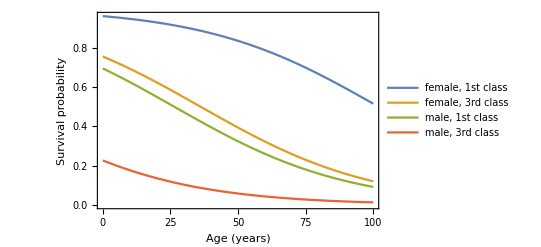

```mathematica
p[class_, age_, sex_] := 
  c[{class, age, sex}, {"Probability", "survived"}];
Plot[{
  p["1st", x, "female"], p["3rd", x, "female"],
  p["1st", x, "male"], p["3rd", x, "male"]}, 
 {x, 0, 100},
 PlotLegends -> {
   "female, 1st class", "female, 3rd class", 
   "male, 1st class", "male, 3rd class"}, 
 Frame -> True,
 FrameLabel -> {"Age (years)", "Survival probability"}]
```

Activity: Create a new classifier that uses the DecisionTree algorithm and see how it performs.

We can also ask Mathematica to determine the best Machine Learning algorithm for us to use, we will do this by not specifying the type of algorithm we want to use, Mathematica will find the best one for us.

```mathematica
dataset = ExampleData[{"MachineLearning", "Titanic"}, "Data"];
c = Classify[dataset]
```

```mathematica
ClassifierInformation[c]
```

Now lets use the classifier that we just made to predict our outcome on the titanic

```mathematica
c [{1, 12, male}]
```